## Rotational wave function

```mathematica
ClearAll["Global`*"]
```

The study for a rotational wave function (its shape and evolution with the azimuthal angle ϕ).
-Graphics-

-> Define the expression of the wave function
-> Create a list of projections M for a given spin
The angle defined in Eq. (4-5) is in fact the azimuthal angle which describes the rotation around the z-axis, according to the picture shown below:
-Graphics-

```mathematica
phiM[phi_,M_]:=1/Sqrt[2π] Exp[ⅈ*M*phi];
projections[I_]:=Table[i,{i,-I,I,1}];
rephi[phi_,M_]:=If[Im[phiM[phi,M]]==0,phiM[phi,M],Re[phiM[phi,M]]];
phisquared[phi_,M_]:=Abs[phiM[phi,M]^2];
```

### Constants

```mathematica
Ifixed=3;
Mfixed=2;
```

### Study the change of φ w.r.t. to the change of azimuthal angle φ and fixed projection M

### Create batch data for a given spin

Given a certain spin value I, the function generateDataFixedM is executed for all its projections M ∈ [-I,I].
The collection of wavefunction components evaluated for the azimuthal angle at fixed M.

```mathematica
generateBatchData[I_]:=Table[generateDataFixedM[M],{M,-I,I,1}];
```

Create function for generating proper legend expressions

```mathematica
legends[data_]:=Table[Style[StringTemplate["M=``"][i],18,Bold,Black],{i,-(Length[data]-1)/2,(Length[data]-1)/2,1}];
```

```mathematica
generateDataFixedM[M_]:=Table[{angle,rephi[angle,M]},{angle,0,π,0.1}];
plotPhiFixedM[I_]:=ListPlot[generateBatchData[I],Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"ϕ [rad]","Re[φ_M(ϕ)]"},Epilog->Inset[Style[StringTemplate["I=``"][I],18,Bold,Black],Scaled[{0.1,0.2}]],PlotRange->Full,LabelStyle->{18,Bold,Black,FontFamily->"Times"},ImageSize->Large,AspectRatio->0.7,PlotLegends->Placed[legends[generateBatchData[I]],Right]];
```

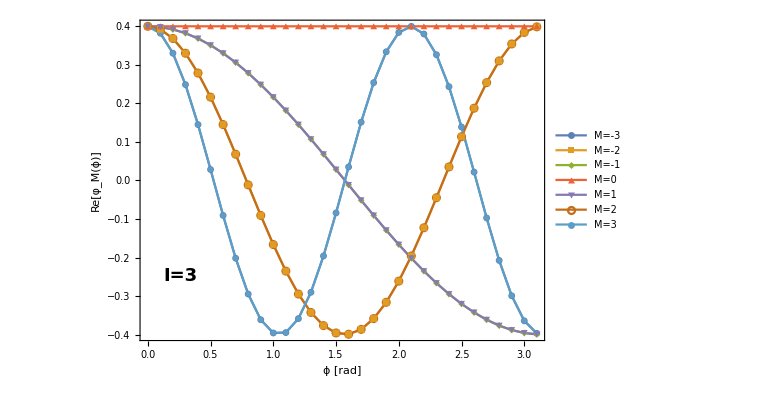

```mathematica
plotPhiFixedM[3]
```